# Vaje iz Mathematice, 2. del

### 1. naloga:

Izračunaj vrednost izraza  30! -20! +110

```mathematica
vr1= 30!-20!+110
```

265252859812188625734300303360110

Kakšna je 10. števka od leve proti desni?

```mathematica
IntegerDigits[vr1][[10]]
```

8

Rezultat razcepi na prafaktorje.

```mathematica
raz1=FactorInteger[vr1]
```

{{2,1},{5,1},{11,3},{41,1},{101,1},{897840721,1},{5360156751159421,1}}

Katero je največje praštevilo v razcepu?

```mathematica
Length[raz1]
```

7

```mathematica
First[Last[raz1]]
```

5360156751159421

Katero praštevilo nastopa v razcepu z najvišjo potenco?

```mathematica
First[Last[Sort[raz1,#1[[2]]< #2[[2]]&]]]
```

11

```mathematica
Reverse[{1,2,3,4}]
Last[Last[Sort[Map[Reverse,raz1]]]]
```

{4,3,2,1}

11

### 2. naloga:

Poišči vse delitelje števila 16524000.

```mathematica
st2=16524000
del2=Divisors[st2]
```

16524000

{1,2,3,4,5,6,8,9,10,12,15,16,17,18,20,24,25,27,30,32,34,36,40,45,48,50,51,54,60,68,72,75,80,81,85,90,96,100,102,108,120,125,135,136,144,150,153,160,162,170,180,200,204,216,225,240,243,250,255,270,272,288,300,306,324,340,360,375,400,405,408,425,432,450,459,480,486,500,510,540,544,600,612,648,675,680,720,750,765,800,810,816,850,864,900,918,972,1000,1020,1080,1125,1200,1215,1224,1275,1296,1350,1360,1377,1440,1500,1530,1620,1632,1700,1800,1836,1944,2000,2025,2040,2125,2160,2250,2295,2400,2430,2448,2550,2592,2700,2720,2754,3000,3060,3240,3375,3400,3600,3672,3825,3888,4000,4050,4080,4131,4250,4320,4500,4590,4860,4896,5100,5400,5508,6000,6075,6120,6375,6480,6750,6800,6885,7200,7344,7650,7776,8100,8160,8262,8500,9000,9180,9720,10125,10200,10800,11016,11475,12000,12150,12240,12750,12960,13500,13600,13770,14688,15300,16200,16524,17000,18000,18360,19125,19440,20250,20400,20655,21600,22032,22950,24300,24480,25500,27000,27540,30375,30600,32400,33048,34000,34425,36000,36720,38250,38880,40500,40800,41310,44064,45900,48600,51000,54000,55080,57375,60750,61200,64800,66096,68000,68850,73440,76500,81000,82620,91800,97200,102000,103275,108000,110160,114750,121500,122400,132192,137700,153000,162000,165240,172125,183600,194400,204000,206550,220320,229500,243000,275400,306000,324000,330480,344250,367200,413100,459000,486000,516375,550800,612000,660960,688500,826200,918000,972000,1032750,1101600,1377000,1652400,1836000,2065500,2754000,3304800,4131000,5508000,8262000,16524000}

```mathematica
Length[del2]
```

288

Katera od njih so praštevila?

```mathematica
Select[del2, PrimeQ]
```

{2,3,5,17}

```mathematica
PrimeQ[1847897]
```

True

S kakšnimi potencami nastopajo v razcepu števila 16524000?

```mathematica
FactorInteger[st2]
```

{{2,5},{3,5},{5,3},{17,1}}

### 3. naloga:

Izračunaj  lim_(x→2) (x^3-4 x^2+2x+4)/(x^5-9x-14)

```mathematica
Limit[(x^3-4x^2+2x+4)/(x^5-9x-14),x->2]
```

-2/71

Izračunaj  lim_(x→0) (arctg (7x))/(arcsin (8x))

```mathematica
Limit[ArcTan[7x]/ArcSin[8x],x->0]
```

7/8

Izračunaj  lim_(x→5) (x^2-25)ctg (π x)

```mathematica
Limit[(x^2-25)*Cot[Pi*x],x->5]
```

10/π

Izračunaj  lim_(x→π) (1+cos x)/(2 √(π x)-π-x)

Izračunaj levo limito:  lim_(x→0^-) |x|ctg x

```mathematica
Limit[Abs[x]*Cot[x],x->0,Direction->"FromBelow"]
```

-1

Izračunaj desno limito:  lim_(x→0^+) |x|ctg x

```mathematica
Limit[Abs[x]*Cot[x],x->0,Direction->"FromAbove"]
```

1

### 4. naloga:

Izračunaj prvi odvod funkcije  y=2sin (2x+1)  cos (x)

```mathematica
D[2Sin[2x+1]Cos[x],x]
```

4 Cos[x] Cos[1+2 x]-2 Sin[x] Sin[1+2 x]

Izračunaj prvi odvod funkcije  y=x ln (2x)

Izračunaj prvi odvod funkcije  y=(3x-2)^(1/3)/(√(2x+1))

```mathematica
D[CubeRoot[3x-2]/Sqrt[2x+1]]
```

(-2+3 x)^(1/3)/(√(1+2 x))

Izračunaj drugi odvod funkcije  y=(x+1)^x

```mathematica
D[D[(x+1)^x,x],x]//Simplify
D[(x+1)^x,{x,2}]//Simplify
```

(1+x)^(-2+x) (2+x+x^2+2 x (1+x) Log[1+x]+(1+x)^2 Log[1+x]^2)

(1+x)^(-2+x) (2+x+x^2+2 x (1+x) Log[1+x]+(1+x)^2 Log[1+x]^2)

### 5. naloga:

Numerično izračunaj ničle polinoma  x^7-2 x^6-x^5-2 x^4+12 x^2-x+1.

```mathematica
resitve5=NSolve[x^7-2 x^6-x^5-2 x^4+12 x^2-x+1==0]
Solve[x^7-2 x^6-x^5-2 x^4+12 x^2-x+1==0]
nicle5=x/. resitve5
```

{{x→-1.37527},{x→-0.356206-1.47367 ⅈ},{x→-0.356206+1.47367 ⅈ},{x→0.040941-0.283889 ⅈ},{x→0.040941+0.283889 ⅈ},{x→1.59494},{x→2.41086}}

{{x→Root-1.38Root[1-#1+12 #1^2-2 #1^4-#1^5-2 #1^6+#1^7&,1]-1.3752699335115919},{x→Root1.59Root[1-#1+12 #1^2-2 #1^4-#1^5-2 #1^6+#1^7&,2]1.5949411250735304},{x→Root2.41Root[1-#1+12 #1^2-2 #1^4-#1^5-2 #1^6+#1^7&,3]2.4108595453371398},{x→Root-0.356-1.47 ⅈRoot[1-#1+12 #1^2-2 #1^4-#1^5-2 #1^6+#1^7&,4]-0.3562064041542111},{x→Root-0.356+1.47 ⅈRoot[1-#1+12 #1^2-2 #1^4-#1^5-2 #1^6+#1^7&,5]-0.3562064041542111},{x→Root0.0409-0.284 ⅈRoot[1-#1+12 #1^2-2 #1^4-#1^5-2 #1^6+#1^7&,6]0.040941035704671946},{x→Root0.0409+0.284 ⅈRoot[1-#1+12 #1^2-2 #1^4-#1^5-2 #1^6+#1^7&,7]0.040941035704671946}}

{-1.37527,-0.356206-1.47367 ⅈ,-0.356206+1.47367 ⅈ,0.040941-0.283889 ⅈ,0.040941+0.283889 ⅈ,1.59494,2.41086}

Katere od teh ničel so realne?

```mathematica
RealQ[x_]:=Element[x,Reals]
Select[nicle5,RealQ]
```

{-1.37527,1.59494,2.41086}

Kakšna je največja absolutna vrednost ničle?

```mathematica
Max[Map[Abs,nicle5]]
```

2.41086

### 6. naloga:

Razcepi polinom  x^7+2 x^6-80 x^5+232 x^4+175 x^3-826 x^2+256x-1056  na linearne in kvadratne faktorje.

```mathematica
Factor[x^7+2 x^6-80 x^5+232 x^4+175 x^3-826 x^2+256x-1056]
```

(-4+x)^2 (-3+x) (2+x) (11+x) (1+x^2)

Razcepi isti polinom na linearne faktorje.

```mathematica
I
```

ⅈ

```mathematica
Factor[x^7+2 x^6-80 x^5+232 x^4+175 x^3-826 x^2+256x-1056,Extension->I]
```

(-4+x)^2 (-3+x) (-ⅈ+x) (ⅈ+x) (2+x) (11+x)

```mathematica
MandelbrotSetPlot[{-0.65+0.47I,-0.4+0.72I},PlotLegends->Automatic]
```

-Graphics-

Faktoriziraj trigonometrični izraz  sin (x)+cos (2x)

```mathematica
TrigFactor[Sin[x]+Cos[2x]]
Factor[Sin[x]+Cos[2x],Trig->True]
```

2 Sin[π/4-x/2]^2 (1+2 Sin[x])

(Cos[x/2]-Sin[x/2])^2 (1+2 Sin[x])

### 7. naloga:

```mathematica
Clear[x]
Clear[y]
```

Definiraj polinom  (x^2* (y-1)-x^3*y^5+(x-1)^7*x *y *(x^2+2x y+y^3))^2  kot novo spremenljivko.

```mathematica
polli7=(x^2*(y-1)-x^3*y^5+(x-1)^7*x*y*(x^2+2x*y+y^3))^2
```

(x^2 (-1+y)-x^3 y^5+(-1+x)^7 x y (x^2+2 x y+y^3))^2

Razširi polinom tako, da dobiš vsoto monomov.

Razvij polinom po potencah x  (koeficienti bodo polinomi v y).

Kakšna je najvišja potenca posameznih spremenljivk, ki se pojavita v polinomu?

```mathematica
Exponent[polli7,{x,y}]
```

{20,10}

### 8.naloga:

Določi vsa realna števila, ki zadoščajo neenačbi  (|x-3|)/(x+1)>√(3-2x)

```mathematica
neen8=Abs[x-3]/(x+1)>Sqrt[3-2x]
Reduce[neen8,Reals]
```

Abs[-3+x]/(1+x)>√(3-2 x)

-1<x<1||1<x≤3/2

```mathematica
MandelbrotSetPlot[{-0.65+0.47I,-0.4+0.72I},MaxIterations->200,ColorFunction->"RedBlueTones"]
```

-Graphics-

### 9. naloga:

Definiraj  (x^2-1)/(x^2-4)  kot funkcijo f spremenljivke x in nariši njen graf na intervalu [-5,5].

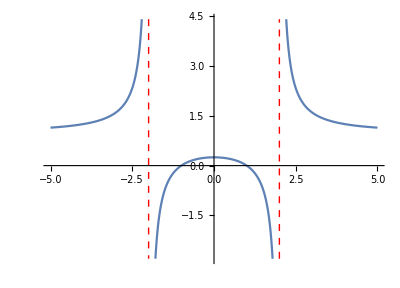

```mathematica
f[x_]:=(x^2-1)/(x^2-4)
Plot[f[x],{x,-5,5},ExclusionsStyle->{{Dashed,Red}},AspectRatio->Automatic]
```

Določi ničle.

Določi pole in razišči obnašanje funkcije v okolici polov.

Izračunaj limiti v neskončnosti.

Določi stacionarne točke.

Določi vrsto stacionarnih točk (lokalni minimum, lokalni maksimum, prevoj).

Določi intervale konveksnosti.

Določi intervale konkavnosti.

### 10. naloga:

Analiziraj funkcijo y=arctg x^2/(x^2-1). Zgleduj se po prejšnji nalogi.

### 11. naloga:

Določi tangento na funkcijo h(x)=sin^2 x-cos x  v točki x=2. Rezultat predstavi s sliko.

```mathematica
Clear[k]
```

```mathematica
h[x_]:=Sin[x]^2-Cos[x]
k=D[h[x],x]/.x->2
n=h[2]-2k
th[x_]:=k*x+n
```

Sin[2]+2 Cos[2] Sin[2]

-Cos[2]+Sin[2]^2-2 (Sin[2]+2 Cos[2] Sin[2])

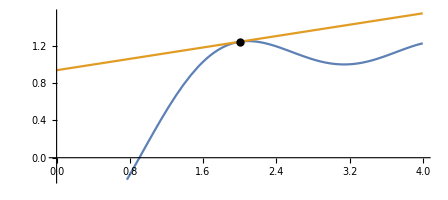

```mathematica
Plot[{h[x],th[x]},{x,0,4},
Epilog->{PointSize[0.015],
Point[{2,h[2]}]},
AspectRatio->Automatic]
```

### 12. naloga:

Dana sta vektorja  (v⃗)_1=(1,2,3)  in  (v⃗)_2=(-3,-2,5). Zapiši ju kot dve spremenljivki.

```mathematica
v1={1,2,3}
v2={-3,-2,5}
```

{1,2,3}

{-3,-2,5}

Izračunaj njun skalarni produkt.

```mathematica
skal12=v1 .v2
```

8

Izračunaj njun vektorski produkt.

```mathematica
vekt12=Cross[v1,v2]
```

{16,-14,4}

Kateri od vektorjev je daljši?

```mathematica
Norm[v1]
Norm[v2]
Max[Norm[v1],Norm[v2]]
```

√14

√38

√38

Sestavi enačbo ravnine, ki gre skozi točko (1,1,1) in ima normalo v smeri vektorskega produkta.

```mathematica
vekt12.{x,y,z}==vekt12.{1,1,1}//Simplify
```

3+7 y==8 x+2 z

### 13. naloga:

Dana je matrika  M=(9 | 2 | -3
3 | 2 | 1
6 | 4 | -1).  Zapiši jo kot spremenljivko.

```mathematica
M={{9,2,-3},{3,2,1},{6,4,-1}}
```

{{9,2,-3},{3,2,1},{6,4,-1}}

```mathematica
M//MatrixForm
```

(9 | 2 | -3
3 | 2 | 1
6 | 4 | -1)

Izračunaj njeno determinanto.

```mathematica
Det[M]
```

-36

Izračunaj njene lastne vrednosti.

```mathematica
Eigenvalues[M]
```

{3 (1+√2),4,3 (1-√2)}

Izračunaj njene lastne vektorje.

```mathematica
Eigenvectors[M]
```

{{-(-6-5 √2)/(6 (1+√2)),-(-2-√2)/(2 (1+√2)),1},{2,7,8},{-(-5+3 √2)/(3 √2 (-1+√2)),-(2-√2)/(2 (-1+√2)),1}}

Ali je matrika diagonalizabilna?

Matriko želimo diagonalizirati. Konstruiraj diagonalno matriko (po diagonali ima lastne vrednosti), prehodno matriko (za stolpce ima lastne vektorje) in inverz prehodne matrike.

```mathematica
DiagM=DiagonalMatrix[Eigenvalues[M]]
DiagM//MatrixForm
```

{{3 (1+√2),0,0},{0,4,0},{0,0,3 (1-√2)}}

(3 (1+√2) | 0 | 0
0 | 4 | 0
0 | 0 | 3 (1-√2))

```mathematica
PrehM=Transpose[Eigenvectors[M]]
PrehM//MatrixForm
Eigenvectors[M]//MatrixForm
```

{{-(-6-5 √2)/(6 (1+√2)),2,-(-5+3 √2)/(3 √2 (-1+√2))},{-(-2-√2)/(2 (1+√2)),7,-(2-√2)/(2 (-1+√2))},{1,8,1}}

(-(-6-5 √2)/(6 (1+√2)) | 2 | -(-5+3 √2)/(3 √2 (-1+√2))
-(-2-√2)/(2 (1+√2)) | 7 | -(2-√2)/(2 (-1+√2))
1 | 8 | 1)

(-(-6-5 √2)/(6 (1+√2)) | -(-2-√2)/(2 (1+√2)) | 1
2 | 7 | 8
-(-5+3 √2)/(3 √2 (-1+√2)) | -(2-√2)/(2 (-1+√2)) | 1)

```mathematica
InveM=Inverse[M]
InveM//MatrixForm
```

{{1/6,5/18,-2/9},{-1/4,-1/4,1/2},{0,2/3,-1/3}}

(1/6 | 5/18 | -2/9
-1/4 | -1/4 | 1/2
0 | 2/3 | -1/3)

Preveri, ali velja pogoj za diagonalizabilnost.

### 14. naloga:

Dana je parametrično podana krivulja  (((3-t) sin t)/(t+1),cos (t) sin (2t)). Definiraj jo kot funkcijo ene spremenljivke.

```mathematica
p[t_]:={(3-t)Sin[t]/(t+1),Cos[t]Sin[2t]}
```

Nariši krivuljo za  t∈[0,5].

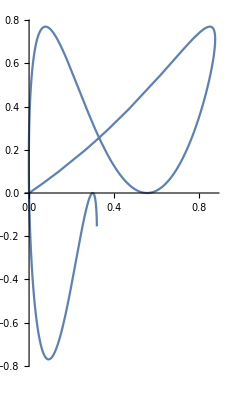

```mathematica
ParametricPlot[p[t],{t,0,5},AspectRatio->Automatic]
```

Krivulja seče samo sebe natanko dvakrat. S pomočjo numeričnega reševanja enačb (FindRoot) poišči približek presečišč. Enačbo nastavi tako da izenačiš krivuljo, parametrizirano s parametrom t, s krivuljo, parametrizirano s parametrom s. Potem s spreminjanjem začetnih približkov parametrov t in s poskusi določiti vrednosti parametrov, pri katerih pride do samopresečič.

```mathematica
resitev1=FindRoot[p[t]==p[s],{t,0},{s,2}]
```

{t→0.130416,s→1.95093}

```mathematica
resitev2=FindRoot[p[t]==p[s],{t,0},{s,3}]
```

{t→-2.79032×10^-20,s→3.14159}

```mathematica
tocka1={t,s}/. resitev1
```

{0.130416,1.95093}

```mathematica
tocka2={t,s}/. resitev2
```

{-2.79032×10^-20,3.14159}

```mathematica
p[t] /. First[resitev1]
p[s] /. Last[resitev1]
```

{0.330126,0.255695}

{0.330126,0.255695}

```mathematica
p[t] /. First[resitev2]
p[s] /. Last[resitev2]
```

{-8.37095×10^-20,-5.58064×10^-20}

{-4.18682×10^-18,2.44929×10^-16}

Iz dobljenih rešitev sestavi točki.

Grafično preveri, ali gre za pravilen izračun.

### 15. naloga:

Naj bodo a⃗, b⃗ in c⃗ vektorji v R^3.
S simboličnim računom dokaži identiteto  a⃗×(b⃗×c⃗)=(a⃗·c⃗)b⃗-(a⃗·b⃗)c⃗

```mathematica
a={a1,a2,a3}
```

{a1,a2,a3}

```mathematica
napisemo enacbo->simplify
```

enacbo napisemo→simplify

### 16. naloga:

Dokaži, da za poljubni 2×2 matriki A in B velja enakost  (A B)^-1=B^-1 A^-1.